```mathematica
ClearAll["Global`*"]  (*two-stage third-order TSRK methods (IM TSRK23)*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["a*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["b*"]
ClearAll["d*"]
nn=4;
e=Table[1,{ii,nn},{i,1}];  e2=Table[1,{ii,2},{i,1}];
v=({{0, 0, a23*bk, a34}});   

A=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, a23, 0}, {0, 0, a23*bk, a34}});   d=({{1, 0}, {0, 1}, {d31, d32}, {d41+d31*bk, d42+d32*bk}});   L=({{-w1}, {0}});  b=({{d41+d31*bk, d42+d32*bk}});
c=A.e+d.L; 
ce=c-e;

C1=DiagonalMatrix[c[[;;,1]]];Ce=DiagonalMatrix[ce[[;;,1]]];
τ2=-((c^2-d.(L^2))/2)+A.c;               τ3=-((c^3-d.(L^3))/6)+A.c^2/2;
τ4=-((c^4-d.(L^4))/4!)+A.c^3/3!;    τ5=-((c^5-d.(L^5))/5!)+A.c^4/4!;
τf2=τ2;   τf3=τ3-τ2;    τf4=τ4-τ3+τ2/2;  τf5=τ5-τ4+τ3/2-τ2/6;
(*τf2=0;   τf3=τ3;    τf4=τ4-τ3;  τf5=τ5-τ4+τ3/2;*)
p0=1-b.e2;  p1=1-b.L+Total[-v.e,2];    p2=(1-b.(L^2))/2+Total[-v.c,2];
p30=    (1-b.(L^3))/3+Total[-v.c^2 ,2];  pp31=Total[v.τ2,2];
(* d31=0; vv1=0; aa21=a21=0; *)(* w1=1;*)
 a21=0;  a22=0;         (*w1=1;*)   (*    *) d32=1-d31;    (*bk=-0.1; *) w1=1;  a34=0.27507783444105344;
c
 p0
sol=Solve[p0==0&&p1==0&&p2==0&&p30==0&&pp31==0 ,{  bk, a23,  d31,d41 ,d42}]  //FullSimplify 
p0/.sol//FullSimplify   
p1/.sol//FullSimplify      p2/.sol//FullSimplify 
p30/.sol//FullSimplify    pp31/.sol//FullSimplify
```

{{-1},{0},{a23-d31},{0.275078+a23 bk-bk d31-d41}}

{{1-bk (1-d31)-bk d31-d41-d42}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{bk→-4.91629,a23→1.13679,d31→1.74189,d41→2.24993,d42→3.66636},{bk→3.10227,a23→0.238796,d31→-0.0540971,d41→0.183712,d42→-2.28598}}

{{{0.}},{{0.}}}

{{{-5.55112×10^-17 FullSimplify}},{{1.11022×10^-16 FullSimplify}}}[{{{-8.88178×10^-16}},{{-1.11022×10^-16}}}]

{-3.66477×10^-16 FullSimplify,1.05834×10^-17 FullSimplify}[{{{-6.66134×10^-16}},{{1.11022×10^-16}}}]

```mathematica
ClearAll["Global`*"]  (*two-stage third-order TSRK methods (IM TSRK23)*)
Remove["Global`*"]
ClearAll["p*"]
ClearAll["a*"]
ClearAll["v*"]
ClearAll["w*"]
ClearAll["b*"]
ClearAll["d*"]
nn=4;
e=Table[1,{ii,nn},{i,1}];  e2=Table[1,{ii,2},{i,1}];
v=({{0, 0, a33, a34}});   v̂=({{0, 0, 0, 0}});

A=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, a23, 0}, {0, 0, a33, a34}});  Â=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});  d=({{1, 0}, {0, 1}, {d31, d32}, {d41, d42}});   L=({{-w1}, {0}});  b=({{d41, d42}});
c=A.e+d.L; ĉ= Â.e; 
ce=c-e;

C1=DiagonalMatrix[c[[;;,1]]];Ce=DiagonalMatrix[ce[[;;,1]]];
τ2=-((c^2-d.(L^2))/2)+A.c+Â.e;               τ3=-((c^3-d.(L^3))/6)+A.c^2/2+Â.c;
τ4=-((c^4-d.(L^4))/4!)+A.c^3/3!+Â.c^2/2!;    τ5=-((c^5-d.(L^5))/5!)+A.c^4/4!+Â.c^3/3!;
τf2=τ2;   τf3=τ3-τ2;    τf4=τ4-τ3+τ2/2;  τf5=τ5-τ4+τ3/2-τ2/6;
(*τf2=0;   τf3=τ3;    τf4=τ4-τ3;  τf5=τ5-τ4+τ3/2;*)
 p0=1-b.e2;  p1=1-b.L+Total[-v.e,2];    p2=(1-b.(L^2))/2+Total[-v.c-v̂.e,2];
p30=    (1-b.(L^3))/3+Total[-v.c^2 -2*v̂.c,2];  pp31=Total[v.τ2,2];
(* d31=0; vv1=0; aa21=a21=0; *)(* w1=1;*)
 a21=0;  a22=0;         (*w1=1;*)   (*    *) d32=1-d31;   d42=1-d41;  (*bk=-0.1; *) (*w1=1;*)
c
 p0
sol=Solve[p0==0&&p1==0&&p2==0&&p30==0&&pp31==0 ,{   a33,a23,  d31,d41 }]  //FullSimplify 
p0/.sol//FullSimplify   
p1/.sol//FullSimplify      p2/.sol//FullSimplify 
p30/.sol//FullSimplify    pp31/.sol//FullSimplify
```

{{-w1},{0},{a23-d31 w1},{a33+a34-d41 w1}}

{{0}}

{{a33→1/w1^2(-w1 (3+w1)+a34 (6+w1 (6+w1))+2 (-1+√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))))),a23→(-2-w1 (3+w1)+a34 (6+w1 (6+w1))+√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))))/(-3 (1+w1)+3 a34 (2+w1)),d31→1/(3 w1 (-1-w1+a34 (2+w1)))(-1-w1 (3+2 w1)+a34 (3+2 w1 (3+w1))+2 √((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1)))),d41→(-2-3 w1-2 w1^2+2 a34 (3+w1 (3+w1))+2 √((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))))/w1^3},{a33→1/w1^2(-w1 (3+w1)+a34 (6+w1 (6+w1))-2 (1+√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))))),a23→-(2+w1 (3+w1)-a34 (6+w1 (6+w1))+√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))))/(-3 (1+w1)+3 a34 (2+w1)),d31→-1/(3 w1 (-1-w1+a34 (2+w1)))(1+w1 (3+2 w1)-a34 (3+2 w1 (3+w1))+2 √((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1)))),d41→1/w1^3(-w1 (3+2 w1)+2 a34 (3+w1 (3+w1))-2 (1+√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1)))))}}

{{{0}},{{0}}}

{{{0}},{{0}}}[{{{0}},{{0}}}]

{0,0}[{{{0}},{{0}}}]

```mathematica
ClearAll["Global`*"]  (*IM TSRK23  A-stable*)
Remove["Global`*"]
a34=0.904813;  w1=1;
ad=√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))) ;

a23=-(2+w1 (3+w1)-a34 (6+w1 (6+w1))+ ad)/(-3 (1+w1)+3 a34 (2+w1));
d31=-(1+w1 (3+2 w1)-a34 (3+2 w1 (3+w1))+2  ad)/(3 w1 (-1-w1+a34 (2+w1)));



a33=(-w1 (3+w1)+a34 (6+w1 (6+w1))-2 (1+ ad))/w1^2;
dd41=(-w1 (3+2 w1)+2 a34 (3+w1 (3+w1))-2 (1+ ad))/w1^3;
dd42=1-dd41; 
 d32=1-d31
bk=a33/a23
d41=dd41-d31*bk
d42=dd42-d32*bk

(*a34=0.904813; a23=1.31366;d41=-0.317113;d31=-0.905601;d42=1.41711;
d32=1-d31;bk=-0.1; 
*)
```

```mathematica
ClearAll["Global`*"]  (*IM TSRK23  A-stable*)
Remove["Global`*"]
ClearAll["v*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
  w1=1;      a21=0;  a22=0;   v1=0;  


ad=√((1+w1)^2 (1+w1+w1^2)+a34^2 (3+w1 (3+w1))^2-a34 (1+w1) (2+w1) (3+w1 (3+2 w1))) ;

a23=-(2+w1 (3+w1)-a34 (6+w1 (6+w1))+ ad)/(-3 (1+w1)+3 a34 (2+w1));
d31=-(1+w1 (3+2 w1)-a34 (3+2 w1 (3+w1))+2  ad)/(3 w1 (-1-w1+a34 (2+w1)));



a33=(-w1 (3+w1)+a34 (6+w1 (6+w1))-2 (1+ ad))/w1^2;
d41=(-w1 (3+2 w1)+2 a34 (3+w1 (3+w1))-2 (1+ ad))/w1^3;
d42=1-d41; 
 d32=1-d31;

b1=d41; b2=d42;v3=a33; v4=a34;  w1=1;

ff=b1/k+b2+((d31/k+d32)/(1-a23*z))(z*v3)+z*v4*k//FullSimplify
sol=Solve[ff==k,{ k}]//FullSimplify
```

1+(6-11 a34+2 √(12-48 a34+49 a34^2))/(3 (-2+3 a34))

6-14 a34+2 (1+√(12+a34 (-48+49 a34)))+(-7+14 a34-2 √(12+a34 (-48+49 a34)))/k+a34 k z+((6-13 a34+2 √(12+a34 (-48+49 a34))) (-2 (3+√(12+a34 (-48+49 a34)))+a34 (11-2 k)+2 √(12+a34 (-48+49 a34)) k) z)/(k (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)))

{{k→(-24+78 a34-63 a34^2-6 √(12+a34 (-48+49 a34))+9 a34 √(12+a34 (-48+49 a34))+12 z-40 a34 z+29 a34^2 z+4 √(12+a34 (-48+49 a34)) z-5 a34 √(12+a34 (-48+49 a34)) z-1/2 √(-4 (-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)) (-5 √(12+a34 (-48+49 a34)) z-6 (7+2 √(12+a34 (-48+49 a34))+3 z)-a34^2 (126+59 z)+a34 (147+18 √(12+a34 (-48+49 a34))+65 z+8 √(12+a34 (-48+49 a34)) z))+4 (6 (4+√(12+a34 (-48+49 a34)))+a34^2 (63-29 z)-4 (3+√(12+a34 (-48+49 a34))) z+a34 (-78-9 √(12+a34 (-48+49 a34))+5 (8+√(12+a34 (-48+49 a34))) z))^2))/((-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)))},{k→(-24+78 a34-63 a34^2-6 √(12+a34 (-48+49 a34))+9 a34 √(12+a34 (-48+49 a34))+12 z-40 a34 z+29 a34^2 z+4 √(12+a34 (-48+49 a34)) z-5 a34 √(12+a34 (-48+49 a34)) z+1/2 √(-4 (-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)) (-5 √(12+a34 (-48+49 a34)) z-6 (7+2 √(12+a34 (-48+49 a34))+3 z)-a34^2 (126+59 z)+a34 (147+18 √(12+a34 (-48+49 a34))+65 z+8 √(12+a34 (-48+49 a34)) z))+4 (6 (4+√(12+a34 (-48+49 a34)))+a34^2 (63-29 z)-4 (3+√(12+a34 (-48+49 a34))) z+a34 (-78-9 √(12+a34 (-48+49 a34))+5 (8+√(12+a34 (-48+49 a34))) z))^2))/((-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)))}}

0.0687364

0.0532022

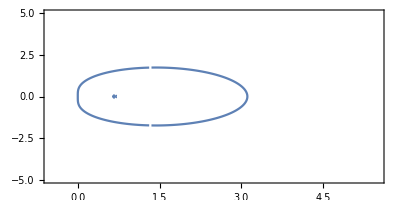

```mathematica
ClearAll["Global`*"]  (*IM TSRK23  A-stable*)
Remove["Global`*"]
ClearAll["x*"]
ClearAll["y*"]
ClearAll["f*"]
ClearAll["z*"]
z=x+I*y;

f1[z_]:=(-24+78 a34-63 a34^2-6 √(12+a34 (-48+49 a34))+9 a34 √(12+a34 (-48+49 a34))+12 z-40 a34 z+29 a34^2 z+4 √(12+a34 (-48+49 a34)) z-5 a34 √(12+a34 (-48+49 a34)) z-1/2 √(-4 (-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)) (-5 √(12+a34 (-48+49 a34)) z-6 (7+2 √(12+a34 (-48+49 a34))+3 z)-a34^2 (126+59 z)+a34 (147+18 √(12+a34 (-48+49 a34))+65 z+8 √(12+a34 (-48+49 a34)) z))+4 (6 (4+√(12+a34 (-48+49 a34)))+a34^2 (63-29 z)-4 (3+√(12+a34 (-48+49 a34))) z+a34 (-78-9 √(12+a34 (-48+49 a34))+5 (8+√(12+a34 (-48+49 a34))) z))^2))/((-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)));
f2[z_]:=(-24+78 a34-63 a34^2-6 √(12+a34 (-48+49 a34))+9 a34 √(12+a34 (-48+49 a34))+12 z-40 a34 z+29 a34^2 z+4 √(12+a34 (-48+49 a34)) z-5 a34 √(12+a34 (-48+49 a34)) z+1/2 √(-4 (-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)) (-5 √(12+a34 (-48+49 a34)) z-6 (7+2 √(12+a34 (-48+49 a34))+3 z)-a34^2 (126+59 z)+a34 (147+18 √(12+a34 (-48+49 a34))+65 z+8 √(12+a34 (-48+49 a34)) z))+4 (6 (4+√(12+a34 (-48+49 a34)))+a34^2 (63-29 z)-4 (3+√(12+a34 (-48+49 a34))) z+a34 (-78-9 √(12+a34 (-48+49 a34))+5 (8+√(12+a34 (-48+49 a34))) z))^2))/((-1+a34 z) (6-(6+√(12+a34 (-48+49 a34))) z+a34 (-9+13 z)));
 

x=100.1; y=0.;
a34=1.2432432432432432;
Abs[f1[z]]//N
Abs[f2[z]]//N

ss1=ContourPlot[N[Abs[f1[z]]]==1.0,{x,-0.5,4.5},{y,-2.5,2.5},AspectRatio->1.2,PlotPoints->100] ;
ss2=ContourPlot[N[Abs[f2[z]]]==1.0,{x,-0.5,4.5},{y,-2.5,2.5},AspectRatio->1.2,PlotPoints->100] ;
Show[ss1,ss2,AspectRatio->0.5]
pp1=ss1[[1,1,1]]//MatrixForm
pp1=ss2[[1,1,1]]//MatrixForm
```